Infinity::indet: Indeterminate expression 0. ∞ encountered.

Infinity::indet: Indeterminate expression 0. (-0.5207+V) ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. (0.+V) ∞ encountered.

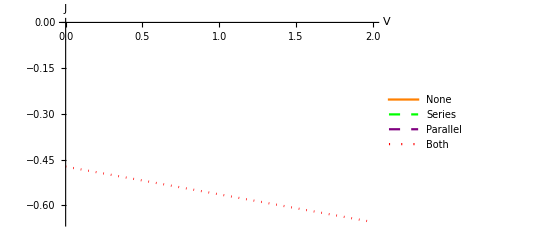

```mathematica
kb=8.61*^-5eV/Kk;(* eV/K *)
kbu=kb Kk/eV;
kbj=1.38*^-23;(*J/K*)
e=1.6*^-19 Cc;(* C *)
eu=e 1/Cc;
Vth=0.79;
T2=300;
Iq=-2.23*^-13;
Isc=-5.207*^-1;
Is1=-Iq;
Is2=-Iq;
(*Is1=Is1(Exp[(eu (V-Iq Rs))/(kbj T2)]-1)+Is2(Exp[(eu(V-Iq Rs))/(2kbj T2)]-1)+Isc+(V-Iq Rs)/Rp;
diode=Isc+Is1(Exp[(eu(V-Iq Rs))/(kbj T2)]);*)
diode=-V/(Rs+Rp)-(ProductLog[(Rs*Is1*Rp*Exp[(Rp(Rs Isc+Rs Is1+V))/(Vth(Rs+Rp))])/(Vth*(Rs+Rp))]*Vth)/Rs+(Rp(Is1+Isc))/(Rs+Rp);
rs=1;
rp=10;
series=diode/.{Rs-> rs,Rp->∞};
parallel=diode/.{Rs-> 0,Rp->rp};
both=diode/.{Rs-> rs,Rp->rp};
none=diode/.{Rs-> 0,Rp->∞};
Plot[{none,series,parallel,both},{V,0,2},PlotRange->{Automatic,0},AxesLabel->{"V","J"},PlotLegends->{"None","Series","Parallel","Both"},PlotStyle-> {{Line,Orange},{Dashed,Green},{Dashed, Purple},{Dotted,Red}}]
```

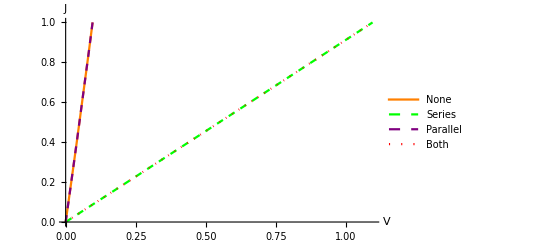

```mathematica
Vth=0.79;
T2=300;
Iq=-2.23*^-13;
Isc=-5.207*^-1;
Is1=-Iq;
Is2=-Iq;
diode=-V/(Rs+Rp)-(ProductLog[(Rs*Is1*Rp*Exp[(Rp(Rs Isc+Rs Is1+V))/(Vth(Rs+Rp))])/(Vth*(Rs+Rp))]*Vth)/Rs+(Rp(Is1+Isc))/(Rs+Rp);
Iss=10+10^-9;
Vth=1;
diode=-Iss+Vth/Rs ProductLog[(Iss Rs)/Vth Exp[(V+Rs Iss)/Vth]];
rs=1;
rp=10;
series=diode/.{Rs-> rs,Rp->10^3};
parallel=diode/.{Rs-> 10^-3,Rp->rp};
both=diode/.{Rs-> rs,Rp->rp};
none=diode/.{Rs-> 10^-3,Rp->10^3};
Plot[{none,series,parallel,both},{V,0,2},PlotRange->{Automatic,0},AxesLabel->{"V","J"},PlotLegends->{"None","Series","Parallel","Both"},PlotStyle-> {{Line,Orange},{Dashed,Green},{Dashed, Purple},{Dotted,Red}}]
```

```mathematica
(Isc+Is1-V/Rp)/(1+Rs/Rp)-(kb T)/Rs ProductLog[(Rs Is1)/(kb T(1+Rs/Rp))Exp[(Rs(Isc+Is1)+V)/(kb T(1+Rs/Rp))]
```

```mathematica
Solve[Voc==k T Log[1-Jsc/js],js]
```

{{js→ConditionalExpression[-Jsc/(-1+ⅇ^(Voc/(k T))), -π<Im[Voc/(k T)]≤π]}}

```mathematica
Jsc=-5.207;
Voc=0.7950707521102732;
-Jsc/(-1+ⅇ^(Voc/(kbu T2)))
```

```mathematica
2.231571428571427*^-13
```

```mathematica
Manipulate[Plot[{-35+1.5*^-12 (-1+ⅇ^(38.71467286101432 V)),-35+1.5*^-12 (-1+ⅇ^(38.71467286101432 (10^rs/1000000+V))),-35+1.5*^-12 (-1+ⅇ^(38.71467286101432 V))+V/10^rp,-35+1.5*^-12 (-1+ⅇ^(38.71467286101432 (10^rs/1000000+V)))+(10^rs/1000000+V)/10^rp},{V,0,1},PlotRange->{Automatic,0},AxesLabel->{"V","J"},PlotLegends->{"None","Series","Parallel","Both"},PlotStyle-> {{Dashed,Orange},Green, Purple,Red}],{{rp,1},-3,1},{rs,3,6}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.795071

-35.

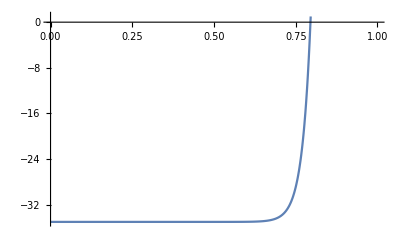

(-35+1.5×10^-12 (-1+ⅇ^(38.7147 V))) V

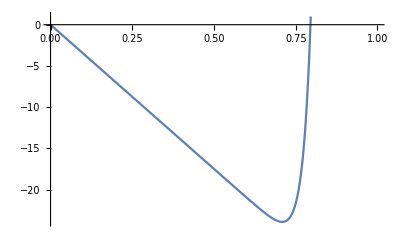

-35+1.5×10^-12 (-1+ⅇ^(38.7147 V))+5.8072×10^-11 ⅇ^(38.7147 V) V

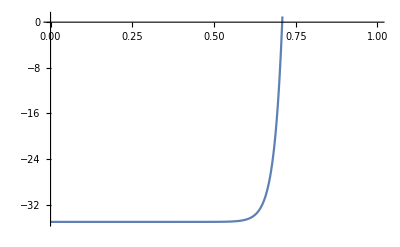

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.708603

-33.7691

0.8599

```mathematica
kbu=8.61*^-5;(* eV/K *)
T2=300;
Iq=-10^-12;
Isc=-35;
Is1=1.5*^-12;
Rs=0;
Rp=∞;

diode=Is1(Exp[(V-Iq Rs)/(kbu T2)]-1)+Isc+(V-Iq Rs)/Rp;
Voc = Solve[diode==0,V][[1,1,2]]
Jsc=diode/.V->0
Plot[diode,{V,0,1},PlotRange->{Automatic,1}]
pow = diode*V
Plot[pow,{V,0,1},PlotRange->{Automatic,1}]
Dpow = D[pow,V]
Plot[Dpow,{V,0,1},PlotRange->{Automatic,1}]
vmp=Reduce[Dpow==0,V,Reals][[2]]
jmp=diode/.V->vmp
FF =(vmp jmp)/(Voc Jsc)
```

```mathematica
diode/.V->0.7
```

-34.1178

```mathematica
Exp[38.71467286101432] (0.025830000000000002+1)-6.027000000000259*^11
```

6.67791×10^16

```mathematica
dif=D[diode,V]
int=Integrate[diode,V]
```

5.8072×10^-11 ⅇ^(38.7147 V)

3.8745×10^-14 ⅇ^(38.7147 V)-35. V

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.795071

1355.01

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{V→-38.7147}}

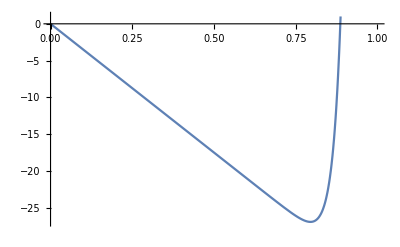

```mathematica
Plot[int,{V,0,1},PlotRange->{Automatic,1}]
```

```mathematica
300-273.15
```

26.85

```mathematica
Solve[diode ==0,V]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{V→0.795071}}

x-ⅇ^(1/10000+Log[x]^2/1000000) x^2

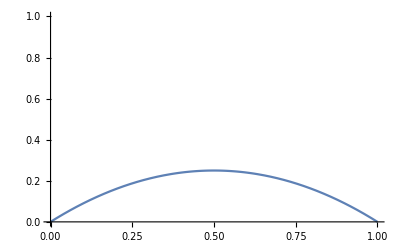

```mathematica
test = x-Exp[10^-6*Log[x]^2+2 Log[x]+10^-4]
Plot[test,{x,0,1},PlotRange->{Automatic,1}]
```